```mathematica
A={{1,2,3,4},{-3,2,-5,13},{1,-2,10,4},{-2,9,-8,25}}
Det[A]
```

{{1,2,3,4},{-3,2,-5,13},{1,-2,10,4},{-2,9,-8,25}}

301

```mathematica
res=DSolve[x y'[x]-2 y[x]==2 x^4,y[x],x]
```

{{y[x]→x^4+x^2 C[1]}}

```mathematica
r[x_]=2+x-x^2
D[r[x], x]
```

2+x-x^2

1-2 x

```mathematica
r[x_]=(3-x^2)^3
Integrate[r[x],x]
```

(3-x^2)^3

27 x-9 x^3+(9 x^5)/5-x^7/7

```mathematica
Solve[{x^2-y^2==3,x^4-y^4==15},{x,y}]
```

{{x→-2,y→-1},{x→-2,y→1},{x→2,y→-1},{x→2,y→1}}

```mathematica
Apart[(x^4-2 x^3+4 x^2-6 x+8)/(x-1)]
```

-3+5/(-1+x)+3 x-x^2+x^3

```mathematica
__________________________________________________________________________________________________________________________________________________
```

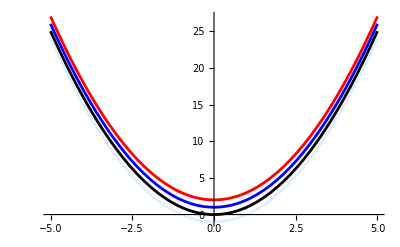

```mathematica
Plot[{x^2,x^2+1,x^2+2,x^2-1},{x,-5,5},PlotStyle->{{Black},{Blue},{Red},{LightBlue}}]
```

{{y→InterpolatingFunction[…]}}

{{y[x]→-2+ⅇ^x}}

InterpolatingFunction[…]

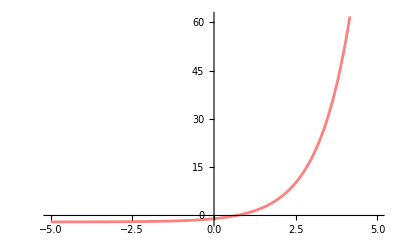

```mathematica
res=NDSolve[{y''[x]-y'[x]==0,y[0]==-1,y'[1]-y[1]==2},y,{x,-10,10}]
DSolve[{y''[x]-y'[x]==0,y[0]==-1,y'[1]-y[1]==2},y[x],x]
f=y/.res⟦1⟧
Plot[f[s],{s,-5,5},PlotStyle->{Pink}]
```

```mathematica
ContourPlot3D[x^2+5 y^2+z^2+2 x y+6 x z+2 y z-2 x+6 y+2 z==0,{x,-10,10},{y,-10,10},{z,-10,10}]
```

-Graphics3D-

```mathematica
___ ___ ___ ___ ___ ___ ___ ___ ___ ___ ___ ___ ___ ___ ___ ___ ___ ___ ___ ___ ___ ___ ___ ___ ___ ___ ___ ___ ___ ___ ___ ___ ___ ___ ___ ___ ___ ___ ___ ___ ___ ___ ___ ___ ___ ___ ___ ___ ___ ___
```

```mathematica
f[x_,a_,b_,c_]:=a x^2+b x + c(*уравнение параболы*)

Manipulate[d=p;
i=0;
tt=Table[p,1];(*здесь хранится просто точка*)
If[f[p[[1]],a,b,c]!=p[[2]] && p[[1]]!=(-b/(2 a)),(*условие на то что это не вершина*){While[i<n,(*условие на количество точек биллиарда*){v={x0,y0}/.FindInstance[y0==f[x0,a,b,c]&& ((b-(d[[2]]-y0)/(d[[1]]-x0))^2 -4a (c+x0 (d[[2]]-y0)/(d[[1]]-x0) - y0))==0 && ((fl==1 && x0>p[[1]])||(fl==0 && x0<p[[1]])) &&(x0==-b/(2a) || (x0!=d[[1]]&&y0!=d[[2]])) ,{x0,y0}](*(х0,у0) - точка касания, второе уравнение отвечает за единственную точку пересечения(берется из приравнивания уравнения параболы и прямой-касательной), третье условие за то справа или слева*), v=v[[1]],v=d+2 (v-d),d=v,tt=Join[tt,{v}],i++}](*прибавляем к начальной точке двойной вектор от нее до точки касания, ставим полученную точку как новую начальную, вписываем ее в таблицу*)}];Show[{Plot[f[x,a,b,c],{x,-100,100}],ListLinePlot[tt]}],{{a,1},-10,20,Appearance->"Labeled"},{{b,0},-20,20,Appearance->"Labeled"},{{c,0},-20,20,Appearance->"Labeled"},{{p,{5,10}},Locator},{n,1,10,1,Appearance->"Labeled"},{fl,{ 1-> "right", 0->"left"}}]
```